# 2. DOMAČA NALOGA

## 1. Naloga

### Daljice

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

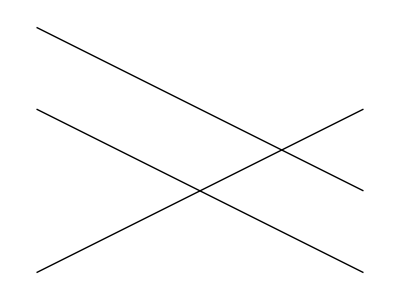

```mathematica
Narisi[d, d2, d3]
```

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

## 2. Naloga

### Presek daljic

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

## 3. Naloga

### N - kotnik

```mathematica
ClearAll[Slika]
```

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
m2 =Append[m1,m1[[1]]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Slika[Mnogokotnik[t__]] := Line[{t}]
Slika [m2]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

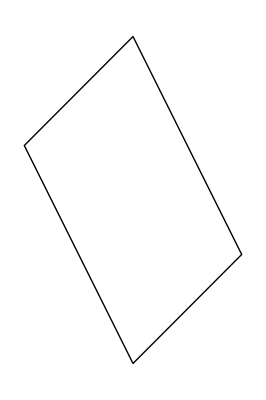

```mathematica
Narisi[m__Mnogokotnik] := Graphics[Slika[m]]
Narisi [m2]
```

```mathematica
PravilniNKotnik[n_,r_] :=Graphics[{Line[Table[{r*Cos[(2Pi*i)/n],r*Sin[(2Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
p5 = PravilniNKotnik[5,2]
```

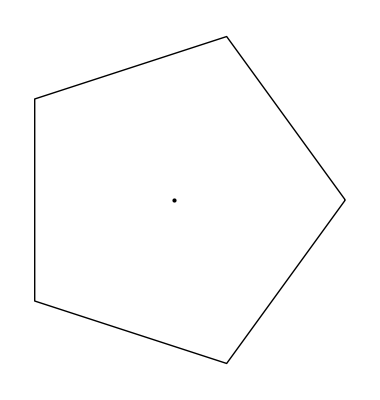
```mathematica
-Graphics-ga
```

```mathematica
PravilniNKotnik[n_,r_,phi_] := Graphics[{Line[Table[{r*Cos[(2Pi*i+phi)/n ],r*Sin[(2Pi*i+phi)/n]},{i,0,n}]],Point[{0,0}]}]
Kotnik = Manipulate[PravilniNKotnik[5,2,phi],{phi,1.5,33}]
```

```mathematica
Daljice[Mnogokotnik[t__]] := Map[Daljica,Partition[{t}, 2,1]]
daljice = Daljice[m2]
```

{Daljica[{{0,0},{1,1}}],Daljica[{{1,1},{0,3}}],Daljica[{{0,3},{-1,2}}],Daljica[{{-1,2},{0,0}}]}

## 4. Naloga

### Presek mnogokotnik & daljica

```mathematica
Presek[m_Mnogokotnikk, d_Daljica]:=Module[{resitev,dal},
del=EnacbaNosilke[d];
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
]
```

## 5. Naloga

### Seznami

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f, sez1,sez2],1]
```

```mathematica
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
f[x_,y_]:=x / y
```

```mathematica
VsiPari[f,{1,2,3},{-9,6,10,2}]
```

{-1/9,1/6,1/10,1/2,-2/9,1/3,1/5,1,-1/3,1/2,3/10,3/2}

```mathematica
g[m1_Mnogokotnika,m2_Mnogotnika]:=Presek[m1,m2]
```

```mathematica
Presek[m1_Mnogokotnika,m2_Mnogkotnika]:=VsiPari[g,m1,m2]
```

## 6. Naloga